```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"data","energyData.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

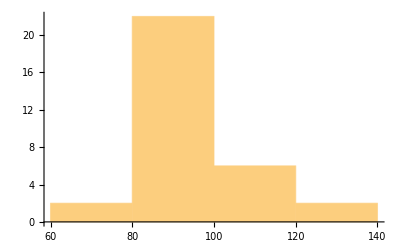
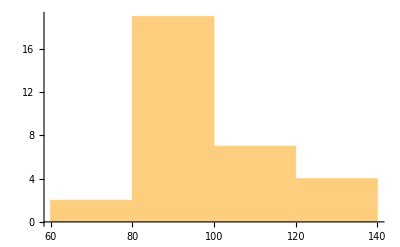
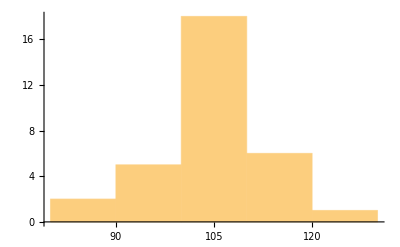
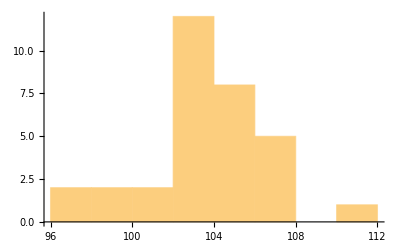
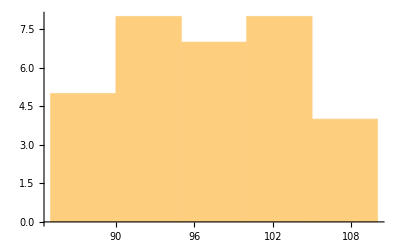

```mathematica
Histogram/@(data⟦1;;5⟧)
```

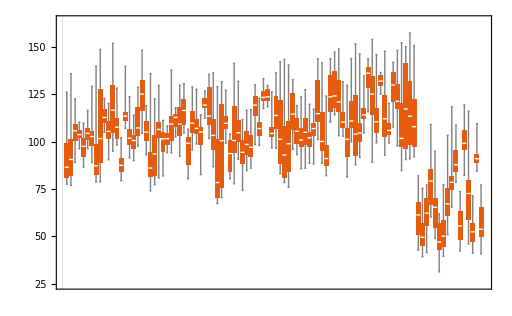

```mathematica
BoxWhiskerChart[data,PerformanceGoal->"Speed",PlotTheme->"Scientific"]
```

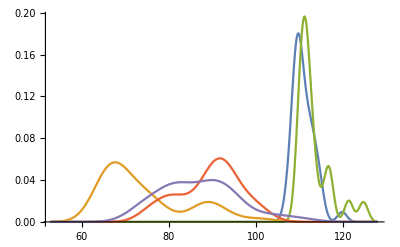

```mathematica
SmoothHistogram[ndata,PlotRange->All]
```